# Dados dos diferentes circuitos de transmissão de energia elétrica

## Antonio Carlos Siqueira de Lima Dezembro 2021

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/acsl/Dropbox/UFRJ/cursos/EEE457-Transmissão_Energia_Elétrica/arquivos_Mma_EEE457

```mathematica
SetOptions[{ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,Joined->True,
Axes-> False,Frame-> True,PlotRange->All];
```

```mathematica
SetOptions[{Plot,LogPlot,LogLinearPlot,LogLogPlot},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,PlotStyle-> Thick,
Axes-> False,Frame-> True];
```

```mathematica
<<LineCableParam2020`
```

Comprimento de todos os circuitos de 500 kV igual a 180 km

## Alguns Dados Importantes

```mathematica
μ = 4. π 10^-7;
ϵ= 8.854 10^-12;
ρs=1000.0; (* resistividade do solo *)
ω= 2. π 60.;
```

### 3/8 EHS

```mathematica
rpr = 4.570 10^-3;
Rdcpr=4.19*10^-3;
```

### Ruddy

```mathematica
r0=7.821 *10^-3 ;(* ⟹ [m] ⟸ *)
r1 = 14.364 10^-3;
ρϕ=29.559 10^-9;  (* [Ω/m] *)
```

### Grossbeak

```mathematica
r0=7.456 *10^-3 ;(* ⟹ [m] ⟸ *)
r1 = 12.573 10^-3;
ρϕ=29.538 10^-9;  (* [Ω/m] *)
```

### Dove

```mathematica
r0=6.988 *10^-3 ;(* ⟹ [m] ⟸ *)
r1 = 11.773 10^-3;
ρϕ=29.567 10^-9;  (* [Ω/m] *)
```

### Penguim

```mathematica
r0=4.123 *10^-3 ;(* ⟹ [m] ⟸ *)
r1 = 7.150 10^-3;
ρϕ=28.554 10^-9;  (* [Ω/m] *)
```

### Leghorn

```mathematica
r0=4.840 *10^-3 ;(* ⟹ [m] ⟸ *)
r1 = 6.7180 10^-3;
ρϕ=29.586 10^-9;  (* [Ω/m] *)
```

### Minorca

```mathematica
r0=4.390 *10^-3 ;(* ⟹ [m] ⟸ *)
r1 = 6.0960 10^-3;
ρϕ=29.579 10^-9;  (* [Ω/m] *)
```

## Configurações analisadas

### 750 kV - Bluejay

```mathematica
db=.475;
xc0= {-15.85,0, 15.85};
xc=Flatten@Outer[Plus,xc0,db Cos[π/4 +#1 π/2]&@Range[0,3]];xc=Flatten[Join[xc,{-14.45,14.45}]];
fc = 20.9;
yc0= {35.9 , 35.9, 35.9}-2/3 fc;
yc1={45.9,45.9}- 2/3 14.7;
yc= Flatten@Outer[Plus,yc0,db Sin[π/4 +#1 π/2]&@Range[0,3]];
yc= Flatten[Join[yc,yc1]];
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.09]},{i,1,Length[xc]}];
o1=tsimples=Show[Graphics[mostra],Axes->False,Frame->Automatic,AspectRatio-> 1,
BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,PlotRange->{Automatic,{10,Max[yc]+5 }},FrameLabel->{Style["Distance [m]",Bold,18],Style["Distance [m]",Bold,18]}]
```

-Graphics-

### Bluejay

```mathematica
r0=8.702 10^3;   (* [m]*)
r1=15.977 *10^-3;
ρϕ=29.544 10^-9;(* Ω/m] *)
Rdc= ρϕ/(π (r1^2-r0^2));
npr = 2;
nb = 4;
```

```mathematica
{Zabc,Yabc}=cZYlt[ω, xc, yc,1/ρs, Rdc, r1, r0,  npr, Rdcpr, rpr,nb];
```

```mathematica
MatrixForm[Zabc 1000]
```

(0.086108+0.649112 ⅈ | 0.0911262+0.352786 ⅈ | 0.0901825+0.301299 ⅈ
0.0911262+0.352786 ⅈ | 0.0868938+0.648218 ⅈ | 0.0911262+0.352786 ⅈ
0.0901825+0.301299 ⅈ | 0.0911262+0.352786 ⅈ | 0.086108+0.649112 ⅈ)

```mathematica
MatrixForm[Yabc 1000]
```

(3.×10^-9+4.53205×10^-6 ⅈ | 0.-7.82373×10^-7 ⅈ | 0.-2.02622×10^-7 ⅈ
0.-7.82373×10^-7 ⅈ | 3.×10^-9+4.64579×10^-6 ⅈ | 0.-7.82373×10^-7 ⅈ
0.-2.02622×10^-7 ⅈ | 0.-7.82373×10^-7 ⅈ | 3.×10^-9+4.53205×10^-6 ⅈ)

### 500 kV Convencional - Rail

```mathematica
xy3={{-11.000,10.736},{-10.771,11.132},{-11.229,11.132},{0.000,10.736},{0.229,11.132},{-0.229,11.132},{11.000,10.736},{10.771,11.132},{11.229,11.132},{-6.000,22.000},{6.000,22.000}};;
```

```mathematica
mostra3={Circle[#,.25]}&/@xy3;
```

```mathematica
xc= Table[First[xy3[[i]]], {i,1,Length[xy3]}];
yc =Table[Last[xy3[[i]]], {i,1,Length[xy3]}];
```

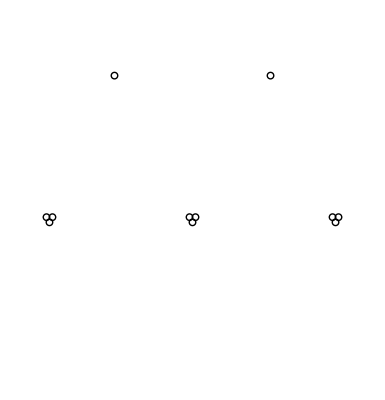

```mathematica
t3=Show[Graphics[mostra3],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-12.1,12.1},{-0.1,25}},FrameLabel->{"distância (m)","distância (m)"}]
```

### Rail

```mathematica
r0=8.702 *10^-3 ;(* ⟹ [m] ⟸ *)
r1 = 14.796 10^-3;
ρϕ=29.538 10^-9;  (* [Ω/m] *)
Rdc= ρϕ/(π (r1^2-r0^2));
npr = 2;
nb = 3;
```

```mathematica
{Zabc,Yabc}=cZYlt[ω, xc, yc,1/ρs, Rdc, r1, r0,  npr, Rdcpr, rpr,nb];
```

```mathematica
MatrixForm[Zabc 1000]
```

(0.117492+0.704873 ⅈ | 0.0971254+0.37396 ⅈ | 0.0951893+0.323444 ⅈ
0.0971254+0.37396 ⅈ | 0.121027+0.70157 ⅈ | 0.0971254+0.37396 ⅈ
0.0951893+0.323444 ⅈ | 0.0971254+0.37396 ⅈ | 0.117492+0.704873 ⅈ)

```mathematica
MatrixForm[Yabc 1000]
```

(3.×10^-9+4.38022×10^-6 ⅈ | 0.-5.73859×10^-7 ⅈ | 0.-1.31661×10^-7 ⅈ
0.-5.73859×10^-7 ⅈ | 3.×10^-9+4.49557×10^-6 ⅈ | 0.-5.73859×10^-7 ⅈ
0.-1.31661×10^-7 ⅈ | 0.-5.73859×10^-7 ⅈ | 3.×10^-9+4.38022×10^-6 ⅈ)

### 500 kV Compacto - Rail

```mathematica
xy4= {{-4.271, 10.771}, {-4.271, 11.229}, {-4.729, 11.229}, {-4.729, 10.771}, {0.229, 15.271},
{0.229, 15.729}, {-0.229, 15.729}, {-0.229, 15.271}, {4.271, 10.771}, {4.271, 11.229},{4.729, 11.229},{4.729, 10.771}, {-3.500, 26.000}, {3.500, 26.000}};
```

```mathematica
mostra4={Circle[#,.25]}&/@xy4;
xc= Table[First[xy4[[i]]], {i,1,Length[xy4]}];
yc =Table[Last[xy4[[i]]], {i,1,Length[xy4]}];
```

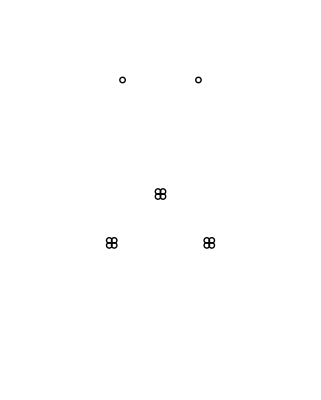

```mathematica
t4=Show[Graphics[mostra4],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-12.1,12.1},{-0.1,30}},FrameLabel->{"distância (m)","distância (m)"}]
```

```mathematica
nb = 4;
{Zabc,Yabc}=cZYlt[ω, xc, yc,1/ρs, Rdc, r1, r0,  npr, Rdcpr, rpr,nb];
```

```mathematica
MatrixForm[Zabc 1000]
```

(0.111144+0.676122 ⅈ | 0.0974557+0.414473 ⅈ | 0.0945825+0.391039 ⅈ
0.0974557+0.414473 ⅈ | 0.117087+0.67063 ⅈ | 0.0974557+0.414473 ⅈ
0.0945825+0.391039 ⅈ | 0.0974557+0.414473 ⅈ | 0.111144+0.676122 ⅈ)

```mathematica
MatrixForm[Yabc 1000]
```

(3.×10^-9+5.08966×10^-6 ⅈ | 0.-1.18527×10^-6 ⅈ | 0.-6.26285×10^-7 ⅈ
0.-1.18527×10^-6 ⅈ | 3.×10^-9+5.11653×10^-6 ⅈ | 0.-1.18527×10^-6 ⅈ
0.-6.26285×10^-7 ⅈ | 0.-1.18527×10^-6 ⅈ | 3.×10^-9+5.08966×10^-6 ⅈ)

### 500 kV - Rail

```mathematica
db=.475;
xc=Flatten@Outer[Plus,{6,11,6+9},db Cos[π/4 +#1 π/2]&@Range[0,3]];
xc=Flatten[Join[xc,-xc]];
yc=Flatten@Outer[Plus,{27.7-4.5,27.7+10-4.5, 27.7-4.5},db Sin[π/4 +#1 π/2]&@Range[0,3]];
yc=Flatten[Join[yc,yc]];
xc=Flatten[Join[xc,{8.8,-8.8}]];
yc=Flatten[Join[yc,{27.7+10+5,27.7+10+5}]];
```

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.09]},{i,1,Length[xc]}];
o1=tsimples=Show[Graphics[mostra],Axes->False,Frame->Automatic,AspectRatio-> 1,
BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,PlotRange->{Automatic,{10,Max[yc]+5 }},FrameLabel->{Style["Distance [m]",Bold,18],Style["Distance [m]",Bold,18]}]
```

-Graphics-

```mathematica
{Zabc,Yabc}=cZYlt[ω, xc, yc,1/ρs, Rdc, r1, r0,  npr, Rdcpr, rpr,nb];
```

```mathematica
MatrixForm[Zabc 1000]
```

(0.10668+0.659443 ⅈ | 0.0931211+0.376972 ⅈ | 0.0891524+0.396939 ⅈ | 0.0900953+0.374309 ⅈ | 0.0929291+0.334321 ⅈ | 0.0890368+0.333217 ⅈ
0.0931211+0.376972 ⅈ | 0.11311+0.653831 ⅈ | 0.092099+0.38076 ⅈ | 0.0929291+0.334321 ⅈ | 0.0958972+0.323343 ⅈ | 0.091734+0.309408 ⅈ
0.0891524+0.396939 ⅈ | 0.092099+0.38076 ⅈ | 0.104752+0.66131 ⅈ | 0.0890368+0.333217 ⅈ | 0.091734+0.309408 ⅈ | 0.0880088+0.307321 ⅈ
0.0900953+0.374309 ⅈ | 0.0929291+0.334321 ⅈ | 0.0890368+0.333217 ⅈ | 0.10668+0.659443 ⅈ | 0.0931211+0.376972 ⅈ | 0.0891524+0.396939 ⅈ
0.0929291+0.334321 ⅈ | 0.0958972+0.323343 ⅈ | 0.091734+0.309408 ⅈ | 0.0931211+0.376972 ⅈ | 0.11311+0.653831 ⅈ | 0.092099+0.38076 ⅈ
0.0890368+0.333217 ⅈ | 0.091734+0.309408 ⅈ | 0.0880088+0.307321 ⅈ | 0.0891524+0.396939 ⅈ | 0.092099+0.38076 ⅈ | 0.104752+0.66131 ⅈ)

```mathematica
MatrixForm[Yabc 1000]
```

(3.×10^-9+5.12268×10^-6 ⅈ | 0.-8.3778×10^-7 ⅈ | 0.-1.1262×10^-6 ⅈ | 0.-7.88134×10^-7 ⅈ | 0.-3.03062×10^-7 ⅈ | 0.-2.16443×10^-7 ⅈ
0.-8.3778×10^-7 ⅈ | 3.×10^-9+4.84752×10^-6 ⅈ | 0.-9.90703×10^-7 ⅈ | 0.-3.03062×10^-7 ⅈ | 0.-3.44091×10^-7 ⅈ | 0.-1.28253×10^-7 ⅈ
0.-1.1262×10^-6 ⅈ | 0.-9.90703×10^-7 ⅈ | 3.×10^-9+4.9221×10^-6 ⅈ | 0.-2.16443×10^-7 ⅈ | 0.-1.28253×10^-7 ⅈ | 0.-7.97511×10^-8 ⅈ
0.-7.88134×10^-7 ⅈ | 0.-3.03062×10^-7 ⅈ | 0.-2.16443×10^-7 ⅈ | 3.×10^-9+5.12268×10^-6 ⅈ | 0.-8.3778×10^-7 ⅈ | 0.-1.1262×10^-6 ⅈ
0.-3.03062×10^-7 ⅈ | 0.-3.44091×10^-7 ⅈ | 0.-1.28253×10^-7 ⅈ | 0.-8.3778×10^-7 ⅈ | 3.×10^-9+4.84752×10^-6 ⅈ | 0.-9.90703×10^-7 ⅈ
0.-2.16443×10^-7 ⅈ | 0.-1.28253×10^-7 ⅈ | 0.-7.97511×10^-8 ⅈ | 0.-1.1262×10^-6 ⅈ | 0.-9.90703×10^-7 ⅈ | 3.×10^-9+4.9221×10^-6 ⅈ)

Calcular a potência natural do circuito e as perdas supondo carregamento igual a impedância característica e alimentação com tensão no terminal emissor igual a 1pu
Investigar o comportamento das matrizes de impedância e admitância de sequências, supondo o circuito transposto

## 500 kV Recapacitado - Rail

```mathematica
xy2={{-7.229, 8.639}, {-7.229, 10.500}, {-6.771, 10.500}, {-6.771, 8.639}, {-0.229, 10.500},
{-0.229, 9.876}, {0.229, 9.876}, {0.229, 10.500}, {7.229, 8.639}, {7.229, 10.500}, {6.771, 10.500},
{6.771, 8.639}, {-5.000, 20.500}, {5.000, 20.500}};
```

```mathematica
mostra2={Circle[#,.25]}&/@xy2;
xc= Table[First[xy2[[i]]], {i,1,Length[xy2]}];
yc =Table[Last[xy2[[i]]], {i,1,Length[xy2]}];
```

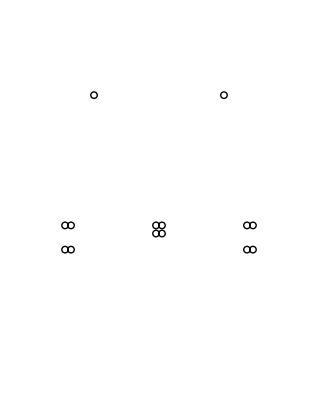

```mathematica
t2=Show[Graphics[mostra2],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-10,10},{-.10,25}},FrameLabel->{"x (m)","y (m)"}]
```

```mathematica
{Zabc,Yabc}=cZYlt[ω, xc, yc,1/ρs, Rdc, r1, r0,  npr, Rdcpr, rpr,nb];
```

```mathematica
MatrixForm[Zabc 1000]
```

(0.114357+0.626587 ⅈ | 0.0990428+0.40516 ⅈ | 0.0976523+0.354856 ⅈ
0.0990428+0.40516 ⅈ | 0.116917+0.661847 ⅈ | 0.0990428+0.40516 ⅈ
0.0976523+0.354856 ⅈ | 0.0990428+0.40516 ⅈ | 0.114357+0.626587 ⅈ)

```mathematica
MatrixForm[Yabc 1000]
```

(3.×10^-9+5.94805×10^-6 ⅈ | 0.-1.21925×10^-6 ⅈ | 0.-3.25131×10^-7 ⅈ
0.-1.21925×10^-6 ⅈ | 3.×10^-9+5.46085×10^-6 ⅈ | 0.-1.21925×10^-6 ⅈ
0.-3.25131×10^-7 ⅈ | 0.-1.21925×10^-6 ⅈ | 3.×10^-9+5.94805×10^-6 ⅈ)

Calcular a potência natural do circuito e as perdas supondo carregamento igual a impedância característica e alimentação com tensão no terminal emissor igual a 1pu

## 500 kV expandido 1

condutor de fase bittern, cabo pararraios 3/8 EHS

```mathematica
xy5={{-5.754,9.543},{-4.496,10.314},{-4.977,11.562},{-6.529,11.562},{-7.009,10.314},{0.000,13.845},{0.866,14.409},{0.535,15.317},{-0.535,15.317},{-0.866,14.409},{5.754,9.543},{4.496,10.314},{4.977,11.562},{6.529,11.562},{7.009,10.314},{-4.000,23.961},{4.000,23.961}};
```

```mathematica
xc= xy5[[1;;,1]];
```

```mathematica
yc= xy5[[1;;,2]];
```

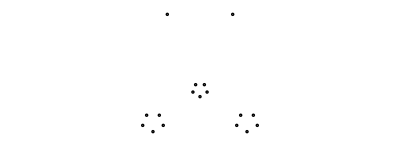

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.125]},{i,1,Length[xc]}];
tsimples=Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-20,20},All},FrameTicks->{{-10,0,10},Automatic,False,False},FrameLabel->{"distância (m)","distância (m)"}]
```

```mathematica
nb = 5;
{Zabc,Yabc}=cZYlt[ω, xc, yc,1/ρs, Rdc, r1, r0,  npr, Rdcpr, rpr,nb];
```

```mathematica
MatrixForm[Zabc 1000]
```

(0.109258+0.583972 ⅈ | 0.0989162+0.405596 ⅈ | 0.095798+0.371846 ⅈ
0.0989162+0.405596 ⅈ | 0.115586+0.598055 ⅈ | 0.0989162+0.405596 ⅈ
0.095798+0.371846 ⅈ | 0.0989162+0.405596 ⅈ | 0.109258+0.583972 ⅈ)

```mathematica
MatrixForm[Yabc 1000]
```

(3.×10^-9+7.18102×10^-6 ⅈ | 0.-1.93222×10^-6 ⅈ | 0.-7.06818×10^-7 ⅈ
0.-1.93222×10^-6 ⅈ | 3.×10^-9+6.87933×10^-6 ⅈ | 0.-1.93222×10^-6 ⅈ
0.-7.06818×10^-7 ⅈ | 0.-1.93222×10^-6 ⅈ | 3.×10^-9+7.18102×10^-6 ⅈ)

Calcular a potência natural do circuito e as perdas supondo carregamento igual a impedância característica e alimentação com tensão no terminal emissor igual a 1pu

## 500 kV expandido 2

condutor de fase grackle, cabo pararraios 3/8 EHS

```mathematica
coordcond={{-5.975},{-5.6499999999999995},{-5.975},{-6.625},{-6.95},{-6.625},{0.32499999999999996},{0.65},{0.32500000000000023},{-0.32499999999999984},{-0.65},{-0.3250000000000003},{6.625},{6.95},{6.625},{5.975},{5.6499999999999995},{5.975},{-8.5},{8.5},{33.59045641596338},{34.62968690050471},{35.668917385046036},{35.668917385046036},{34.62968690050471},{33.59045641596338},{34.09045641596338},{35.12968690050471},{36.168917385046036},{36.168917385046036},{35.12968690050471},{34.09045641596338},{33.59045641596338},{34.62968690050471},{35.668917385046036},{35.668917385046036},{34.62968690050471},{33.59045641596338},{42.32968690050471},{42.32968690050471},{-6.3},{34.62968690050471},{0.29340277777777785},{0.42250000000000004},{0.},{35.12968690050471},{0.29340277777777785},{0.42250000000000004}};
```

```mathematica
xc= coordcond[[1;;20,1]];
yc= coordcond[[21;;,1]];
```

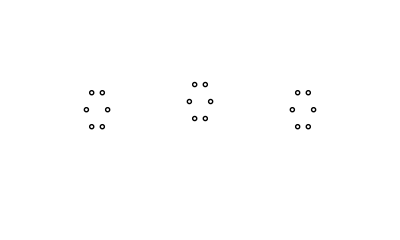

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.125]},{i,1,Length[xc]}];
tsimples=Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-10,10},{28.0,40}},FrameTicks->{{-10,0,10},{30,35,40},False,False},FrameLabel->{"distância (m)","distância (m)"}]
```

```mathematica
nb = 6;
{Zabc,Yabc}=cZYlt[ω, xc, yc,1/ρs, Rdc, r1, r0,  npr, Rdcpr, rpr,nb];
```

```mathematica
MatrixForm[Zabc 1000]
```

(0.111632+0.588971 ⅈ | 0.100553+0.412206 ⅈ | 0.0998673+0.361985 ⅈ
0.100553+0.412206 ⅈ | 0.111981+0.588256 ⅈ | 0.100553+0.412206 ⅈ
0.0998673+0.361985 ⅈ | 0.100553+0.412206 ⅈ | 0.111632+0.588971 ⅈ)

```mathematica
MatrixForm[Yabc 1000]
```

(3.×10^-9+6.47095×10^-6 ⅈ | 0.-2.47082×10^-6 ⅈ | 0.-7.28741×10^-7 ⅈ
0.-2.47082×10^-6 ⅈ | 3.×10^-9+7.30771×10^-6 ⅈ | 0.-2.47082×10^-6 ⅈ
0.-7.28741×10^-7 ⅈ | 0.-2.47082×10^-6 ⅈ | 3.×10^-9+6.47095×10^-6 ⅈ)

Calcular a potência natural do circuito e as perdas supondo carregamento igual a impedância característica e alimentação com tensão no terminal emissor igual a 1pu

## LT 500 kV expandido 3

```mathematica
nfase=3;
nb=5;
npr=2;
ncond=nfase*nb+npr;
```

dados dos condutores obtidos a partir do arquivo LT500kV baseado na torre de 400kV Portela para a Africa

```mathematica
xy6={{-6.722,9.543},{-5.739,10.918},{-6.115,13.139},{-7.330,13.139},{-7.706,10.918},{0.000,10.622},{0.750,11.250},{0.465,12.267},{-0.465,12.267},{-0.750,11.250},{6.722,9.543},{5.739,10.918},{6.115,13.139},{7.330,13.139},{7.706,10.918},{5.000,23.941},{-5.000,23.941}};
```

```mathematica
xc= xy6[[1;;,1]];
yc= xy6[[1;;,2]];
```

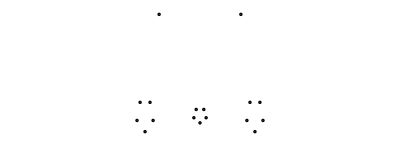

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.125]},{i,1,Length[xc]}];
tsimples=Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-20,20},All},FrameTicks->{{-10,0,10},Automatic,False,False},FrameLabel->{"distância (m)","distância (m)"}]
```

```mathematica
{Zabc,Yabc}=cZYlt[ω, xc, yc,1/ρs, Rdc, r1, r0,  npr, Rdcpr, rpr,nb];
```

```mathematica
MatrixForm[Zabc 1000]
```

(0.109718+0.570959 ⅈ | 0.0970808+0.409354 ⅈ | 0.0961778+0.359353 ⅈ
0.0970808+0.409354 ⅈ | 0.111204+0.603535 ⅈ | 0.0970808+0.409354 ⅈ
0.0961778+0.359353 ⅈ | 0.0970808+0.409354 ⅈ | 0.109718+0.570959 ⅈ)

```mathematica
MatrixForm[Yabc 1000]
```

(3.×10^-9+7.4518×10^-6 ⅈ | 0.-2.08649×10^-6 ⅈ | 0.-5.36242×10^-7 ⅈ
0.-2.08649×10^-6 ⅈ | 3.×10^-9+7.10292×10^-6 ⅈ | 0.-2.08649×10^-6 ⅈ
0.-5.36242×10^-7 ⅈ | 0.-2.08649×10^-6 ⅈ | 3.×10^-9+7.4518×10^-6 ⅈ)

Calcular a potência natural do circuito e as perdas supondo carregamento igual a impedância característica e alimentação com tensão no terminal emissor igual a 1pu

## 345kV - Ruddy

```mathematica
nfase = 3;
nb = 2;
npr = 2;

r0=7.821 *10^-3 ;
r1 = 14.364 10^-3;
ρϕ=29.559 10^-9;
Rdc= ρϕ/(π (r1^2-r0^2));

rpr = 4.570 10^-3;
Rdcpr=4.19*10^-3;

μ = 4. π 10^-7;
ϵ= 8.854 10^-12;
ρs=1000.0; 
ω= 2. π 60.;

xy1={{-7.229,10.5}, {-6.771, 10.500}, {-0.229, 10.500}, {0.229, 10.500}, {7.229, 10.500},
{6.771, 10.500}, {-5.000, 20.500}, {5.000, 20.500}};
```

```mathematica
mostra1={Circle[#,.25]}&/@xy1;
```

```mathematica
t1=Show[Graphics[mostra1],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-10.1,10.1},{0,25}},FrameLabel->{"distância (m)","distância (m)"}]
```

-Graphics-

-Graphics-

```mathematica
xc= xy1[[1;;,1]];
yc= xy1[[1;;,2]];

{Zabc,Yabc}=cZYlt[ω, xc, yc,1/ρs, Rdc, r1, r0,  npr, Rdcpr, rpr,nb];

MatrixForm[Zabc 1000]
```

(0.131486+0.74797 ⅈ | 0.0997481+0.405547 ⅈ | 0.0986202+0.354267 ⅈ
0.0997481+0.405547 ⅈ | 0.133464+0.746103 ⅈ | 0.0997481+0.405547 ⅈ
0.0986202+0.354267 ⅈ | 0.0997481+0.405547 ⅈ | 0.131486+0.74797 ⅈ)

Set::shape: Lists {Zabc,Yabc} and cZYlt[ω,Symbol[],Symbol[],1/ρs,Rdc,r1,r0,2,Rdcpr,rpr,2] are not the same shape.

## LT 230 kV circuito 1

condutor de fase Grossbeak, pararraios 3/8” EHS

```mathematica
xc={-7.5, 0, 7.5, -4.7, 4.7};
yc= {21,21,21,25, 25}-2/3 {12.8, 12.8, 12.8, 8.85, 8.85};
```

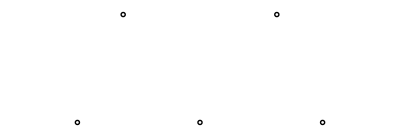

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.125]},{i,1,Length[xc]}];
tsimples=Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-10,10},All},FrameTicks->{{-10,-5, 0,5, 10},Automatic,False,False},FrameLabel->{"distância (m)","distância (m)"}]
```

## LT 230 kV circuito 2

condutor de fase Grossbeak, pararraios 3/8” EHS

```mathematica
xc={-3.8, 3.8, -3.8, -2.4, 2.4};
yc= {28.1,31.1,28.1+5.9,28.1+5.9+7.8,28.1+5.9+7.8}-2/3 {14.6, 14.6, 14.6, 8.7, 8.7};
```

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.125]},{i,1,Length[xc]}];
tsimples=Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-10,10},All},FrameTicks->{{-10,-5, 0,5, 10},Automatic,False,False},FrameLabel->{"distância (m)","distância (m)"}]
```

-Graphics-

## LT 230 kV Circuito Duplo

condutor de fase Grossbeak, pararraios 3/8” EHS

```mathematica
yc={22.15185227641591,28.15185227641591,34.15185227641591,22.15185227641591,28.15185227641591,34.15185227641591,39.15185227641591,39.15185227641591};
```

```mathematica
xc={-4.3,-4.3,-4.3,4.3,4.3,4.3,-3.8,3.8};
```

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.125]},{i,1,Length[xc]}];
tsimples=Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-10,10},All},FrameTicks->{{-10,-5, 0,5, 10},Automatic,False,False},FrameLabel->{"distância (m)","distância (m)"}]
```

-Graphics-